```mathematica
fulldata= Import["C:\\Users\\Jesus Enrique\\Documents\\Wolfram Desktop\\Population1.csv"];
FiltRegInd[ind_]:=GatherBy[Select[fulldata,#[[6]]==ind&],First];
```

```mathematica
sumcountries[list_,init_]:= Table[Total@@(Replace[#,Except[_?NumberQ]-> 0,{1}]& /@{list[[reg,All,ano]]}),{reg,1,6},{ano,init,Length[list[[1,1]]]}];
```

```mathematica
multi [list1_,list2_]:= Table[(list1[[reg,count,ano]]*list2[[reg,count,ano]]),{reg,1,6},{count,1,Length[list1[[reg]]]},{ano,7,Length[list1[[1,1]]]}];
Regiones = Tally[fulldata[[2;;,1]]][[1;;6,1]];
```

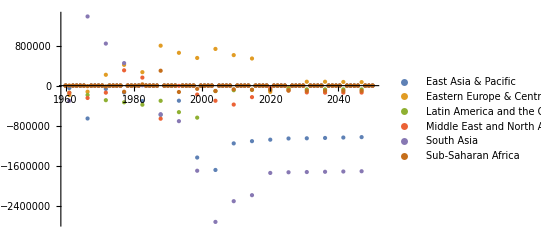

```mathematica
countrypop = FiltRegInd["SP.POP.TOTL"];
indicador = FiltRegInd["SM.POP.NETM"];

regpop = sumcountries[countrypop,7];
mult = multi[countrypop,indicador];
rel = Table[mult[[reg,count,ano]]/regpop[[reg,ano]],{reg,1,6},{count,1,Length[mult[[reg]]]},{ano,7,Length[mult[[1,1]]]}];
ponderado = sumcountries[rel,1];


a =ListPlot[ponderado,PlotRange->All,PlotLegends->Regiones,DataRange->{1960,2050}, Joined->False, PlotStyle->PointSize[Medium]]
```

```mathematica
Export["fertility.pdf",a]
```

fertility.pdf